```mathematica
HtoD = {6.899*10^-5,5.891*10^-5,0.002272,0.00279};
comp = {0.0001658, 0.007027,0.008389,0.8255};
DtoH = {5.069*10^-5,5.078*10^-5,0.002224,0.002226};
tot = {0.09326,0.1005,0.1054,0.9155};

HtoD2 = {6.208*10^-5,6.202*10^-5,0.002461,0.002523};
comp2 = {0.0001668, 0.007733,0.02362,2.356};
DtoH2 = {5.862*10^-5,5.446*10^-5,0.002572,0.002737};
tot2 = {0.104,0.1116,0.1293,2.463};
```

```mathematica
ListLogPlot[{HtoD, DtoH, comp, tot}, Joined->True, PlotLabels->{"Host to Device","Device to Host","Computation","Total"}]
```

-Graphics-

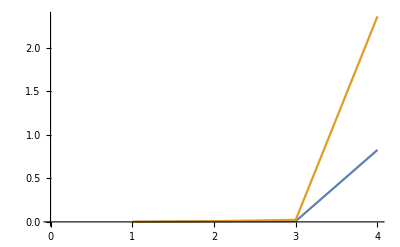

```mathematica
ListPlot[{comp,comp2}, Joined->True]
```